FittedModel[0.673718-0.000372457 x-0.0000399952 «1»+«1»+1.08323×10^-8 x^4-9.46257×10^-11 x^5]

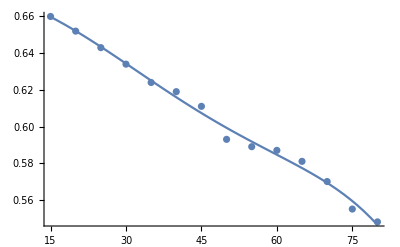

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{T→Root[-1366944790696718326107724529363498406217547950831632887893975+2028957564689692516273711075949310701109777085955173512700395 V+755698435599605522484644113108761643378980850921024668660 #1+81148565371899787353963717338341065590975019294842344965 #1^2-98001782392753279266802018333461761100243518360891917 #1^3-21978287071202418042156245062110191873484911229592725 #1^4+191991539025847618138035743654647962243929186542935 #1^5&,1]},{T→Root[-1366944790696718326107724529363498406217547950831632887893975+2028957564689692516273711075949310701109777085955173512700395 V+755698435599605522484644113108761643378980850921024668660 #1+81148565371899787353963717338341065590975019294842344965 #1^2-98001782392753279266802018333461761100243518360891917 #1^3-21978287071202418042156245062110191873484911229592725 #1^4+191991539025847618138035743654647962243929186542935 #1^5&,2]},{T→Root[-1366944790696718326107724529363498406217547950831632887893975+2028957564689692516273711075949310701109777085955173512700395 V+755698435599605522484644113108761643378980850921024668660 #1+81148565371899787353963717338341065590975019294842344965 #1^2-98001782392753279266802018333461761100243518360891917 #1^3-21978287071202418042156245062110191873484911229592725 #1^4+191991539025847618138035743654647962243929186542935 #1^5&,3]},{T→Root[-1366944790696718326107724529363498406217547950831632887893975+2028957564689692516273711075949310701109777085955173512700395 V+755698435599605522484644113108761643378980850921024668660 #1+81148565371899787353963717338341065590975019294842344965 #1^2-98001782392753279266802018333461761100243518360891917 #1^3-21978287071202418042156245062110191873484911229592725 #1^4+191991539025847618138035743654647962243929186542935 #1^5&,4]},{T→Root[-1366944790696718326107724529363498406217547950831632887893975+2028957564689692516273711075949310701109777085955173512700395 V+755698435599605522484644113108761643378980850921024668660 #1+81148565371899787353963717338341065590975019294842344965 #1^2-98001782392753279266802018333461761100243518360891917 #1^3-21978287071202418042156245062110191873484911229592725 #1^4+191991539025847618138035743654647962243929186542935 #1^5&,5]}}

```mathematica
data={
{15,0.660},
{20,0.652},
{25,0.643},
{30,0.634},
{35,0.624},
{40,0.619},
{45,0.611},
{50,0.593},
{55,0.589},
{60,0.587},
{65,0.581},
{70,0.570},
{75,0.555},
{80,0.548}
};
fit=LinearModelFit[data, {1, x, Power[x, 2], Power[x, 3], Power[x, 4], Power[x, 5]}, x]

Show[
ListPlot[data],
Plot[fit[T], {T, Min[data[[All, 1]]],  Max[data[[All, 1]]]}]
]

Solve[fit[T]==V, T]//Expand
```